# Computing for Mathematical Physics

## Exercises 3: Rules and Patterns

```mathematica
Clear["Global`*"]
```

Click on the line above and press ⇧+⌤ to restart the exercises with any previously held definitions cleared from the memory.

Alternatively, one can restart the Mathematica kernel, which has the same effect, by selecting Evaluation→Quit Kernel→Local from the drop-down menu. Another way to quit the kernel is to type Quit[] in an input cell and then evaluate it by pressing ⇧+⌤.

You are encouraged to use Mathematica's built-in help in the course of these exercises.
Note that you will likely find Head and FullForm useful in the later questions.

## Tips

ReplaceAll, by far most commonly used in the short-hand slash-dot form, someExpression/.someReplacementRules , is one of the most useful, most powerful, commands in Mathematica, you are strongly advised to learn it well.

Mathematica can abort an ongoing evaluation by selecting Evaluation→Abort Evaluation from the drop-down menu. Another way to halt the current cell evaluation is to hit Alt+. on Windows/Linux, or ⌘+. on a Mac. 

Use these evaluation abort keys/options if you find an evaluation is taking much longer than expected, indicating that there is some problem with the input you have supplied, or if you notice an error in your code while it is evaluating. Generally speaking, with perhaps just one or two exceptions, no cell evaluation in this course should take more than 2 mins; i.e. if one finds that a cell is taking more than 2 mins to evaluate, it is likely that your code has an error of some kind.

Note that aborting an evaluation is not the same as quitting the kernel. Quitting the kernel erases all user-defined objects from the memory (expressions, functions, numerical values), whereas aborting the evaluation of a cell leaves all of the memory intact.

Mathematica is case sensitive. 

For example, should you define a variable matrix in your code, you must refer to/access it by typing matrix rather than, e.g. Matrix. If you try to refer to, or access, matrix by typing Matrix you will either be accessing something which is completely undefined, or other than what you meant to access.

Mathematica’s internal functions all start with capital letters.

To help distinguish your code and variables from those internal to Mathematica we therefore recommend starting all user-defined variable and function names with a lowercase letter.

All functions in Mathematica, both internal and user-defined, have their arguments enclosed in single square brackets, e.g. Sin[x], Cos[x], Plot[...], etc.

Round brackets are instead reserved for the usual bracketing of operations, indicating an evaluation order for the various components of an expression, e.g. 2(x+4+Sin[x])^2+Cos[y], etc.

It is good practice to use variables names which are both intuitive and meaningful. If variable names end up comprising of more than one word or abbreviation, we maintain readability by using either camelCase or  snake case.

camelCase variables have words/abbreviations distinguished form one another by capitals, e.g. someVariable.

snake case variables have words/abbreviations separated by a letter space entered as  Esc _ Esc , e.g. some variable.

N.B. In Mathematica a letter space is not the same as a regular underscore. A regular underscore is simply entered as _. A letter space is entered as  Esc _ Esc . Regular underscores have a particularly special meaning in Mathematica, as we shall see in the coming classes, and so they cannot be used within variable names: only letter space can be used in that context ( Esc _ Esc ).

If distinguishing between letter spaces and regular underscores seems too much to take in, please keep things simple and just adopt camelCase.

## Handy Keyboard Shortcuts

In the longer term, you will certainly find it more efficient to learn at least a few very useful keyboard short-cuts, to avoid having to use the mouse and palettes. Short-cuts for superscript, square-root, pi, ⅇ, and ∞ are especially useful (next subsection).

The material in the subsections below is purely intended as a help, and it contains no questions.

### Frequently used mathematical notation

To use the palette and mouse to enter things like superscripts, integrals, etc, go to the drop-down menu at the top of the screen and select Palettes → Basic Math Assistant .

While it's fine to use the palettes to help enter expressions, particularly on meeting Mathematica for the first time(s), many people find it much more useful and faster in the long-run to be able to enter everything from the keyboard, without any need to go to the mouse.

Some frequently used quick keyboard formulations are shown in the grey box below.
These are generally quite intuitive, and require only a very small investment of time to become fluent in; this pays dividends.

-Graphics-

[Copied from https://reference.wolfram.com/language/tutorial/MathematicalAndOtherNotation.html .]

### Switching from input cells to other cell format types, e.g. text cells

Changing the style of a cell (Input/Text) can be done via the drop-down menu at the top of the screen: Format → Style → Input/Text.

Note that Mathematica only interprets the contents of input cells as code to be processed and run. The contents of text cells is not interpreted as code by Mathematica, and is therefore left as-is. (Aside: one should be careful therefore, when entering code, to be clear that the cell you are working with is indeed an input cell and not a text cell. If in doubt, clicking Format → Style and looking for the ✓ will reveal the currently selected cell’s format type.)

By default, all new cells are input cells. However, writing text cells is essential for communicating the purpose and meaning of code appearing in the input cells to the reader.

Alternatively, the next grey box below shows handy short-key entries for quickly changing the cell style format directly from the keyboard, avoiding the mouse: Alt+7 is especially useful, as it enables us to write text cells like this one, which one will do somewhat frequently later in this course.

Note, on a Mac, you would need to swap the Alt buttons below for ⌘.

-Graphics-

These and further keyboard shortcuts can be found here https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html .

### Greek letters

Entering Greek letters couldn’t really be more easy.
Typically, you just type Esc, then the first letter in the name of the Greek letter you want to print, then Esc again:

-Graphics-
See here for further details: https://reference.wolfram.com/language/tutorial/InputAndOutputInNotebooks.html#14875 .

### Less frequently used mathematical notation

One would typically tend to write the relevant long-hand Mathematica command instead of using the keyboard escape sequences below, for integrals etc.

This is often because, at least in the case of integrals and sums, one often needs to provide Mathematica some helpful assumptions about the nature of parameters appearing in the integrand (real / imaginary / positive / negative / bigger-than-some-other-parameter / ... etc) in order for it to proceed to a meaningful answer.

We only really point these out below as they are fairly intuitive too, despite the caveat above.

## Introduction to rules and patterns

### 1. Solving a system of quadratic equations

a) Solve the following system of two quadratic simultaneous equations for x and y:
	  P x^2 +  Q y^2 = 0
	  R x^2 +  S y   = 1.

```mathematica
(* Enter your solution here. *)
Equation1= P*x^2+ Q*y^2==0
Equation2 = R*x^2+ S*y == 1
solutions = Solve[{Equation1,Equation2}, {x,y}]
```

P x^2+Q y^2==0

R x^2+S y==1

{{x→-(√(2/R-(P S^2)/(Q R^2)-(√(-P S^2 (4 Q R-P S^2)))/(Q R^2)))/(√2),y→((P S^2)/(Q R)+(√(P S^2 (-4 Q R+P S^2)))/(Q R))/(2 S)},{x→(√(2/R-(P S^2)/(Q R^2)-(√(-P S^2 (4 Q R-P S^2)))/(Q R^2)))/(√2),y→((P S^2)/(Q R)+(√(P S^2 (-4 Q R+P S^2)))/(Q R))/(2 S)},{x→-√(1/R-(P S^2)/(2 Q R^2)+(√(-4 P Q R S^2+P^2 S^4))/(2 Q R^2)),y→((P S^2)/(Q R)-(√(P S^2 (-4 Q R+P S^2)))/(Q R))/(2 S)},{x→√(1/R-(P S^2)/(2 Q R^2)+(√(-4 P Q R S^2+P^2 S^4))/(2 Q R^2)),y→((P S^2)/(Q R)-(√(P S^2 (-4 Q R+P S^2)))/(Q R))/(2 S)}}

b) Take the third set of solutions and check that they satisfy the initial equations.

```mathematica
(* Enter your solution here. *)
Simplify[{Equation1,Equation2}/.solutions[[3]]]
```

{True,True}

c) Take the third set of solutions and find numerical values for x and y, with P→2, Q→3, R→4, S→5.

```mathematica
(* Enter your solution here. *)
solutions[[3]]/.{P->2, Q->3, R->4, S->5}
```

{x→-ⅈ/(√6),y→1/3}

d) Finally, let us sanity-check that all solutions obtained in part a), do indeed satisfy the original system of equations. Take the original system of equations, and use ReplaceAll, in the shorthand slash-dot form, i.e. someExpression/.someReplacements, to replace x and y by each of their four possible solutions. Wrap the latter output inside Simplify. If each set of solutions is valid, one should obtain a list of four sublists of the form {True, True}. (You are encouraged to glance over the last one-or-two examples in the Examples section of the local or online help for ReplaceAll: https://reference.wolfram.com/language/ref/ReplaceAll.html .)

```mathematica
(* Enter your solution here. *)
Table[Simplify[{Equation1,Equation2}/.solutions[[i]]], {i,1,4}]
```

{{True,True},{True,True},{True,True},{True,True}}

### 2. Solving a system of differential equations

Solve the coupled differential equations (a first-order formulation of the van der Pol equation, describing a non-linear oscillator)
         dx/dt= y
   dy/dt= μ (1-x^2)y - x
numerically for μ=1/2 and initial values x[0]=0 and y[0]=2 for values of t between 0 and 20.

• Use ParametricPlot to produce a graph of y(t) against x(t) over the same range.

```mathematica
(* Enter your solution here. *)
s=NDSolve[{x'[t]==y[t], y'[t] == μ*(1-x[t]^2)*y[t]-x[t], x[0]==0, y[0]==2},{x,y},{t,0,20}]/. μ->1/2;
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

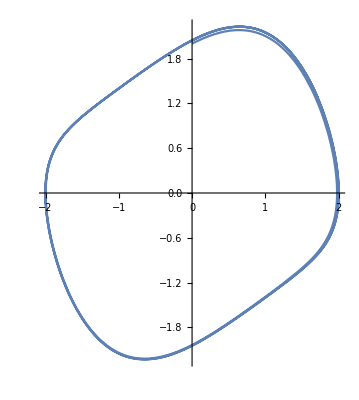

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s], {t,0,20}]
```

### 3. Elementary matrix manipulation using rules

Set up the matrix  { {l,m,n}, {o,p,q}, {r,s,t}, {u,v,w}, {x,y,z} }. Use a rule to swap rows 3 and 4.

```mathematica
(* Enter your solution here. *)
Clear["Global`*"]
matrix = {{l,m,n},{o,p,q},{r,s,t}, {u,v,w},{x,y,z}};
matrix/. {a_ ,b_ , c_ , d_, e___ }-> {a,b,d,c,e}
```

{{l,m,n},{o,p,q},{u,v,w},{r,s,t},{x,y,z}}

### 4. Recursive function definition via replacement rules

The Fibonacci numbers satisfy the recurrence relation  F_n=F_(n-1)+F_(n-2) with F_1=1 and  F_2=1. Thus the first few numbers in the sequence are 1,1,2,3,5,8,13,21.  Set up a rule-based scheme for evaluating the nth Fibonacci number and find the 9th Fibonacci number.

```mathematica
(* Enter your solution here. *)
fibonaccirule = {fibonacci[1]->1, fibonacci[2]->1, fibonacci[n_]->fibonacci[n-1]+fibonacci[n-2]};
fibonacci[9]//.fibonaccirule
Fibonacci[9]
```

34

34

### 5. Using FullForm to analyse and debug replacement rules

FullForm analysis of replacement rules.

a) Code the replacement rule  s[-x_]:>-s[x] and apply it to s[-a], s[-3], and s[-3.0]. You should find that the rule works for s[-a], but not s[-3] or  s[-3.0].

```mathematica
(* Enter your solution here. *)
replodd = s[-x_] :>-s[x]
s[-a]/.replodd
s[-3]/.replodd
s[-3.0]/.replodd
```

s[-x_]:>-s[x]

-s[a]

s[-3]

s[-3.]

b) Use FullForm to examine, i) the rule itself, ii) s[-a], iii) s[-3], iv) s[-3.0]. Hence, determine why the rule works in the s[-a] case, but fails for s[-3] and s[-3.0]. Write one or two sentences clearly explaining the latter in a text cell.

```mathematica
(* Enter your solution here. *)
FullForm[replodd = s[-x_] :>-s[x]]
FullForm[s[-a]]
FullForm[s[-3]]
FullForm[s[-3.0]]
```

RuleDelayed[s[Times[-1,Pattern[x,Blank[]]]],Times[-1,s[x]]]

s[Times[-1,a]]

s[-3]

s[-3.]

The rule does not work for -3 or -3.0 as it does not recognise them as -1 multiplied by its positive number but rather as a separate number, like with -a, where its full form includes a head of Times multiplied by -1.

c) What do you expect that this rule will do to s[1-x] and s[-1-x] and why?

(* Enter your solution here. *)
It will not process either 1-x or -1-x as the first element does not have the right Head that is multiplied by -1 and the same with the -1-x.

```mathematica
s[1-x]/.replodd
s[-1-x]/.replodd
```

s[1-x]

s[-1-x]

### 6. Complex conjugation via replacement rules

Write a replacement rule for complex conjugation of a complex number. Test it on Exp[ⅈ x] and 5a+2ⅈ b. Assume that x, a and b are real. 

Mathematica, of course, has a built-in function for performing complex conjugation, called Conjugate[...], but here we merely aim to test our knowledge of rules, in a familiar setting, where we know, well, what the answer should be.

Recall that in Mathematica both uppercase I and ⅈ (short-key, Esc i i Esc) can be used to represent√-1.) 

You may find that applying the reveal-all FullForm[...] function, to any expressions which the rule is to be applied to, useful for constructing the rule in the first place. It may also be useful for correcting your rule, in the event that you run into problems.

```mathematica
(* Enter your solution here. *)
conjugation = Complex[a_,b_] :> Complex[a,-b]
Exp[ⅈ x]/.conjugation
5a+2ⅈ b /.conjugation
```

Complex[a_,b_]:>Complex[a,-b]

ⅇ^(-ⅈ x)

5 a-2 ⅈ b

### 7. Union operation via replacement rules

Write a rule which is similar to the built-in Union function, but which does not reorder the elements in the list. It should merely drop any second and subsequent occurrences of any element.  Test your function on the following list

		piDigits=Drop[Characters[ToString[N[π,100]]],{2}];

You will obviously need to enter the above command for piDigits in an input cell and evaluate it with ⇧+⌤.

```mathematica
(* Enter your solution here. *)
piDigits = Drop[Characters[ToString[N[π, 100]]],{2}];
```

{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4,6,2,6,4,3,3,8,3,2,7,9,5,0,2,8,8,4,1,9,7,1,6,9,3,9,9,3,7,5,1,0,5,8,2,0,9,7,4,9,4,4,5,9,2,3,0,7,8,1,6,4,0,6,2,8,6,2,0,8,9,9,8,6,2,8,0,3,4,8,2,5,3,4,2,1,1,7,0,6,8}

```mathematica
duplicaterule = {a___, b_, b_, c___}->{a,b,c};
piDigits//.duplicaterule
```

{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4,6,2,6,4,3,8,3,2,7,9,5,0,2,8,4,1,9,7,1,6,9,3,9,3,7,5,1,0,5,8,2,0,9,7,4,9,4,5,9,2,3,0,7,8,1,6,4,0,6,2,8,6,2,0,8,9,8,6,2,8,0,3,4,8,2,5,3,4,2,1,7,0,6,8}

### 8. Data compression via replacement rules

In this exercise we will write rules implementing the data compression method known as run-length encoding.

For every run of repeated characters in a data string, the aim is to replace the run by a list of the form {character, number of repeats}.

The data string we wish to compress is comprised of the first 100 digits of Euler’s constant.

	eulerDigits = Map[ToString,RealDigits[N[EulerGamma,100]][[1]]]

a) Code and evaluate the above expression for eulerDigits in an input cell.

```mathematica
(* Enter your solution here. *)
eulerDigits = Map[ToString,RealDigits[N[EulerGamma,100]][[1]]]
```

{5,7,7,2,1,5,6,6,4,9,0,1,5,3,2,8,6,0,6,0,6,5,1,2,0,9,0,0,8,2,4,0,2,4,3,1,0,4,2,1,5,9,3,3,5,9,3,9,9,2,3,5,9,8,8,0,5,7,6,7,2,3,4,8,8,4,8,6,7,7,2,6,7,7,7,6,6,4,6,7,0,9,3,6,9,4,7,0,6,3,2,9,1,7,4,6,7,4,9,5}

b) First write a rule to convert each entry of eulerDigits to the form {character,1}.

```mathematica
(* Enter your solution here. *)
convertrule = a_String-> {a,1}
eulerDigits/.convertrule
```

a_String→{a,1}

{{5,1},{7,1},{7,1},{2,1},{1,1},{5,1},{6,1},{6,1},{4,1},{9,1},{0,1},{1,1},{5,1},{3,1},{2,1},{8,1},{6,1},{0,1},{6,1},{0,1},{6,1},{5,1},{1,1},{2,1},{0,1},{9,1},{0,1},{0,1},{8,1},{2,1},{4,1},{0,1},{2,1},{4,1},{3,1},{1,1},{0,1},{4,1},{2,1},{1,1},{5,1},{9,1},{3,1},{3,1},{5,1},{9,1},{3,1},{9,1},{9,1},{2,1},{3,1},{5,1},{9,1},{8,1},{8,1},{0,1},{5,1},{7,1},{6,1},{7,1},{2,1},{3,1},{4,1},{8,1},{8,1},{4,1},{8,1},{6,1},{7,1},{7,1},{2,1},{6,1},{7,1},{7,1},{7,1},{6,1},{6,1},{4,1},{6,1},{7,1},{0,1},{9,1},{3,1},{6,1},{9,1},{4,1},{7,1},{0,1},{6,1},{3,1},{2,1},{9,1},{1,1},{7,1},{4,1},{6,1},{7,1},{4,1},{9,1},{5,1}}

c) Write a rule that replaces pairs of successive elements of the form, e.g., {character,number1}, {character,number2}, with a single element {character,number1+number2}. Demonstrate the encoding, using the latter two rules, on eulerDigits.

```mathematica
(* Enter your solution here. *)
combinerule = {n___,{b_,c_}, {b_, d_}, m___} -> {n,{b, d+c},m};
f=eulerDigits/.convertrule//.combinerule
```

{{5,1},{7,2},{2,1},{1,1},{5,1},{6,2},{4,1},{9,1},{0,1},{1,1},{5,1},{3,1},{2,1},{8,1},{6,1},{0,1},{6,1},{0,1},{6,1},{5,1},{1,1},{2,1},{0,1},{9,1},{0,2},{8,1},{2,1},{4,1},{0,1},{2,1},{4,1},{3,1},{1,1},{0,1},{4,1},{2,1},{1,1},{5,1},{9,1},{3,2},{5,1},{9,1},{3,1},{9,2},{2,1},{3,1},{5,1},{9,1},{8,2},{0,1},{5,1},{7,1},{6,1},{7,1},{2,1},{3,1},{4,1},{8,2},{4,1},{8,1},{6,1},{7,2},{2,1},{6,1},{7,3},{6,2},{4,1},{6,1},{7,1},{0,1},{9,1},{3,1},{6,1},{9,1},{4,1},{7,1},{0,1},{6,1},{3,1},{2,1},{9,1},{1,1},{7,1},{4,1},{6,1},{7,1},{4,1},{9,1},{5,1}}

d) Write a rule which undoes the latter encoding. Show that by applying this rule to the encoded data from part c), one recovers exactly the original eulerDigits list: test the equality with the ‘==’ operator.

```mathematica
(* Enter your solution here. *)
decoderule = {n___, {b_,c_},m___}:> {n,Sequence@@ConstantArray[b,c],m };
decode =f//.decoderule ;
decode ==eulerDigits
```

True

### 9. Pattern search with positional information using a delayed rule

The following list holds the first 10000 digits of Euler’s constant

	eulerDigits = RealDigits[N[EulerGamma,10000]][[1]];
	
Code the latter in an input cell and evaluate it with ⇧+⌤.

Use a rule to locate the first occurrence of the sequence 3,4,5, returning the answer in the form {number of digits before the sequence, {3,4,5}, number of digits after the sequence}.

```mathematica
(* Enter your solution here. *)
```

```mathematica
eulerDigits = RealDigits[N[EulerGamma,10000]][[1]];
```

```mathematica
locaterule = {a___, 3,4,5, b___}:> {Length[{a}], {3,4,5}, Length[{b}]};
eulerDigits/.locaterule
```

{1055,{3,4,5},8942}

K. Hamilton, J. Bhamrah, A.H. Harker — UCL
Last revision 10:57 29 Nov 2022